# Basics of Mathematica

## Shift Enter

```mathematica
2+2
```

4

## Equal Signs = vs. := vs. == vs. ===

```mathematica
Simplify[Sin[x]^2+ Cos[x]^2]
```

1

```mathematica
Simplify[Sin[x]^2+Cos[x]^2](*Ctrl + 6*)
```

1

```mathematica
s[x_]=Simplify[x+1] (*Computes the function now. The underscore x_ indicates that x is a variable.*); (*; stops mathematica from displaying the output*)
```

```mathematica
s2[x_]:=Simplify[x+1] (*Do not evaluate anything until I tell you what x is. Using always delay can make things extremely slow.*)
```

```mathematica
s[Cos[x]^2+Sin[x]^2]
```

1+Cos[x]^2+Sin[x]^2

```mathematica
s2[Cos[x]^2+Sin[x]^2]
```

2

```mathematica
2==3 (*== Compares)
```

False

```mathematica
a==b
```

a==b

```mathematica
a===b (*=== is a really strong comparison*)
```

False

```mathematica
Solve[x+1==x^2,x]
```

{{x→1/2 (1-√5)},{x→1/2 (1+√5)}}

```mathematica
Simplify
```

```mathematica
Solve
```

```mathematica
Factor[x^2-1]
```

(-1+x) (1+x)

## Lists

```mathematica
list = {a,b,c}
```

{a,b,c}

```mathematica
MatrixForm[list]
```

(a
b
c)

```mathematica
matrix={{a,b},{c,d}}
```

{{a,b},{c,d}}

```mathematica
matrix2 = {{A,B},{C,D}}
```

{{A,B},{C,D}}

```mathematica
matrix.matrix2
```

{{a A+b C,a B+b D},{A c+C d,B c+d D}}

```mathematica
MatrixForm[matrix.matrix2]
```

(a A+b C | a B+b D
A c+C d | B c+d D)

```mathematica
MatrixForm[matrix]
```

(a | b
c | d)

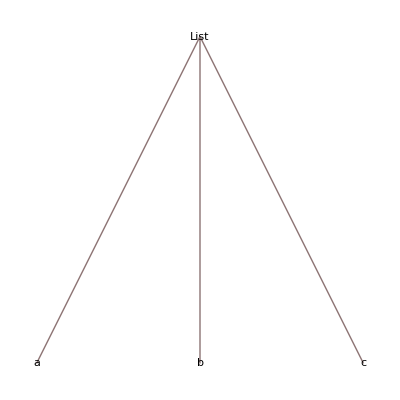

```mathematica
TreeForm[list]
```

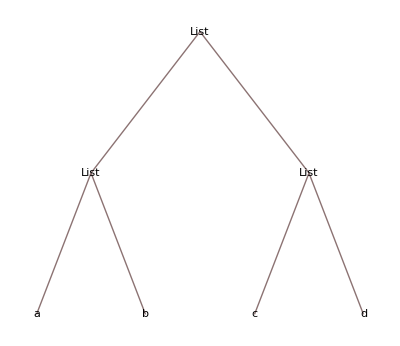

```mathematica
TreeForm[matrix]
```

```mathematica
FullForm[list]
```

List[a,b,c]

```mathematica
{a,{b,c},d}
```

{a,{b,c},d}

```mathematica
FullForm[{a,{b,c},d}]
```

List[a,List[b,c],d]

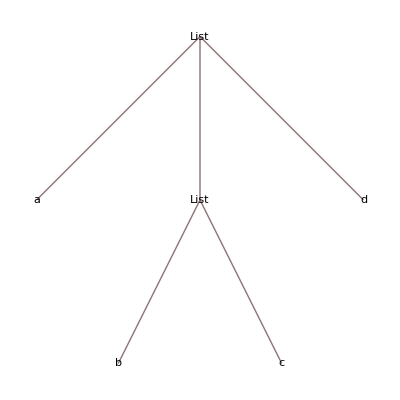

```mathematica
TreeForm[{a,{b,c},d}]
```

```mathematica
Flatten[{a,{b,c},d}]
```

{a,b,c,d}

```mathematica
list[[1]]
```

a

```mathematica
list[[1;;2]]
```

{a,b}

```mathematica
list[[-1]]
```

c

```mathematica
list[[1;;3]]
```

{a,b,c}

```mathematica
{a,{b,c},d}[[2,1]]
```

b

## Substitutions

```mathematica
x/(x^2+1)/.x->Zeta[3]
```

Zeta[3]/(1+Zeta[3]^2)

```mathematica
Zeta[2]
```

π^2/6

```mathematica
N[Zeta[2]]
```

1.64493

```mathematica
x/(x^2+1)
```

x/(1+x^2)

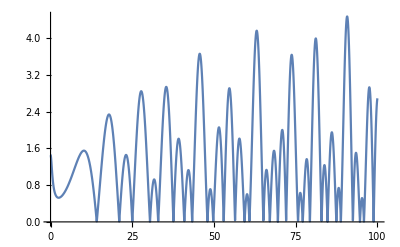

```mathematica
Plot[Abs[Zeta[1/2+ⅈ z]],{z,0,100}]
```

```mathematica
FindRoot[Zeta[1/2+ⅈ z],{z,20}]
```

{z→21.022+1.00542×10^-14 ⅈ}

```mathematica
I==ⅈ
```

True

```mathematica
I===ⅈ
```

True

```mathematica
a=3
b=3
a===b
```

3

3

True

```mathematica
?FindRoot
```

FindRoot[f,{x,x_0}] searches for a numerical root of f, starting from the point x=x_0.
FindRoot[lhs==rhs,{x,x_0}] searches for a numerical solution to the equation lhs==rhs. 
FindRoot[{f_1,f_2,…},{{x,x_0},{y,y_0},…}] searches for a simultaneous numerical root of all the f_i.
FindRoot[{eqn_1,eqn_2,…},{{x,x_0},{y,y_0},…}] searches for a numerical solution to the simultaneous equations eqn_i.

```mathematica
1+x(1+x(1+x))/. 1+x->1
```

1+x (1+x)

```mathematica
1+x(1+x(1+x))//. 1+x->1
```

1

## Delayed Replacement

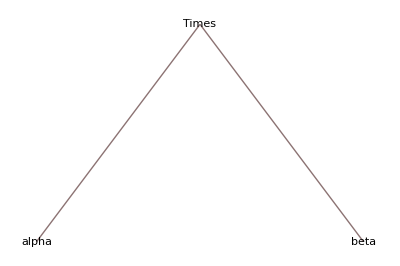

```mathematica
alpha beta // TreeForm
```

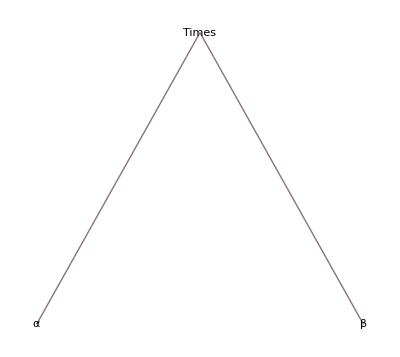

```mathematica
α β // TreeForm
```

```mathematica
alpha === α
```

False

```mathematica
π
```

π

```mathematica
N[π]
```

3.14159

```mathematica
N[α]
```

α

```mathematica
Exp[1-((1+π)2-2-π)/π]/. Exp[x_]->Exp[Simplify[x]]
```

ⅇ^(1-(-2-π+2 (1+π))/π)

We can use :> for delayed replacement

```mathematica
Exp[1-((1+π)2-2-π)/π]/. Exp[x_]:> Exp[Simplify[x]]
```

1

```mathematica
s3[Cos[x]^2+Sin[x]^2]
```

s3[Cos[x]^2+Sin[x]^2]

```mathematica
s2[Cos[x]^2+Sin[x]^2]
```

2

## Apply, Map

```mathematica
Cos[π]
```

-1

```mathematica
Cos@π
```

-1

```mathematica
π//Cos
```

-1

```mathematica
N@Cos@π//ArcSin
```

-1.5708

```mathematica
f1[x_]=Cos[x]+Exp[x];
```

```mathematica
f4=Cos[#1]+Exp[#1]&;
```

```mathematica
f1[y]
```

ⅇ^y+Cos[y]

```mathematica
f4[y]
```

ⅇ^y+Cos[y]

```mathematica
π//f4
```

-1+ⅇ^π

```mathematica
(Cos[#1]+Exp[#1]&)@5
```

ⅇ^5+Cos[5]

```mathematica
5//(Cos[#1]+Exp[#1]&)
```

ⅇ^5+Cos[5]

```mathematica
Cos[x]^2+Sin[x]^2//Simplify[#1+1]&
```

2

```mathematica
Cos[x]^2+Sin[x]^2//Simplify[#+1]&
```

2

```mathematica
S = Simplify[#]&
```

Simplify[#1]&

```mathematica
S[Cos[x]^2+Sin[x]^2]
```

1

## Distribute and Headers

```mathematica
{a,b,c,d}//FullForm
```

List[a,b,c,d]

```mathematica
h@{a,b,c,d}//FullForm
```

h[List[a,b,c,d]]

```mathematica
h/@{a,b,c,d}
```

{h[a],h[b],h[c],h[d]}

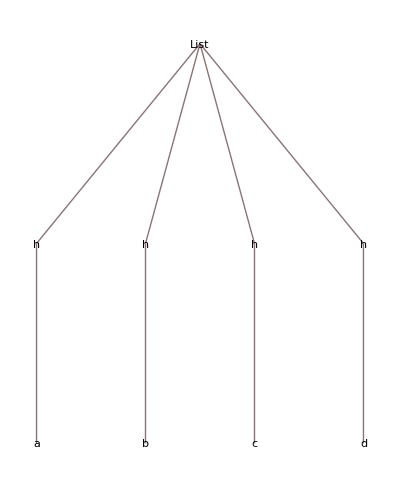

```mathematica
h/@{a,b,c,d}//TreeForm
```

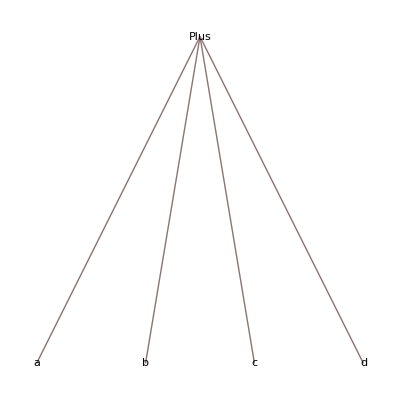

```mathematica
a+b+c+d//TreeForm
```

```mathematica
h/@(a+b+c+d)
```

h[a]+h[b]+h[c]+h[d]

```mathematica
Sin@@Cos[x]
```

Sin[x]

```mathematica
Plus @@ {a,b,c,d}
```

a+b+c+d

```mathematica
Times @@ {a,b,c,d}
```

a b c d

## Patterns

```mathematica
f[2,3]+f[3]/.f[x_]->0
```

f[2,3]

```mathematica
f[2,3]+f[3]/.f[x_,y_]->0
```

f[3]

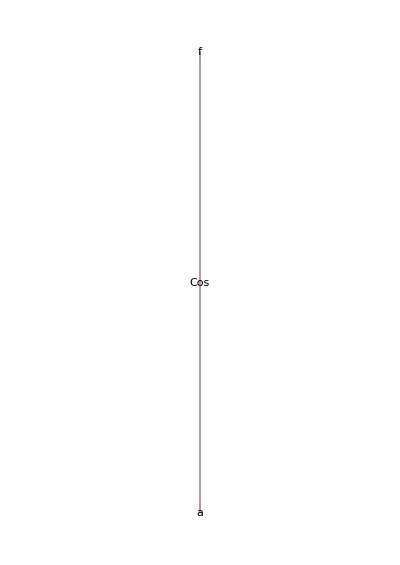

```mathematica
f[Cos[a]]//TreeForm
```

```mathematica
f[2,3]+f[3]/.f[x__]->0
```

0

```mathematica
f[1,2,3,4]+f[2,3,4]+f[3,4]f[3,5]+f[5]+f[4]/.f[a_,4]->0
```

f[4]+f[5]+f[2,3,4]+f[1,2,3,4]

```mathematica
f[1,2,3,4]+f[2,3,4]+f[3,4]f[3,5]+f[5]+f[4]/.f[a__,4]->0
```

f[4]+f[5]

```mathematica
f[1,2,3,4]+f[2,3,4]+f[3,4]f[3,5]+f[5]+f[4]/.f[a___,4]->0
```

f[5]

```mathematica
Cos[x+1](x+1)+Sin[x]/.x+1->y
```

y Cos[y]+Sin[x]

```mathematica
f[1,2,3,4]+f[Cos[y],Cos[y],4]+f[3,5,4]+f[3,5]+f[5]+f[4]/. f[a_,b_,4]:>If[!a==b,0,f[a,b,4]]
```

f[4]+f[5]+f[3,5]+f[Cos[y],Cos[y],4]+f[1,2,3,4]

```mathematica
g[x]=x^2
```

x^2

```mathematica
g[5]
```

g[5]

```mathematica
g[x_]=x^2
```

x^2

```mathematica
g[5]
```

25

## Extra